# Rapport Inlämning 1

Seema Bashir , TIDAB, sfbashir@kth.se
Esra Salman , TIDAB, esras@kth.se

Uppgift 1: Polynomekvation

## Sammanfattning

### Uppgift

Hitta lösningarna till polynomekvationen: 2 x^4-74/3 x^3+253/6 x^2+111/2 x-105=0. 
Rita också grafen för polynomet och markera nollställen med en röd punkt.

### Resultat

Lösningsmängd:

LM ={-3/2,3/2,7/3,10}

Visualisering:

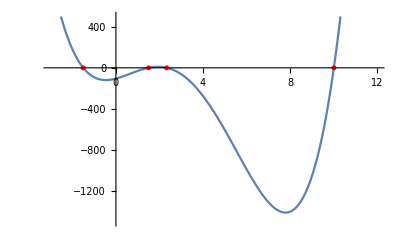

## Kod

För att bestämma lösningen till ekvationen används funktionen: “solve”. För att därefter grafiskt representera ekvationen används: “plot”.

```mathematica
solve[ 2 x^4-74/3 x^3+253/6 x^2+111/2x-105==0]
f[x_]:=2 x^4-74/3 x^3+253/6 x^2+111/2x-105

Plot[f[x],{x,-3.,12.},PlotRange->{-1500,500},
Epilog->{Red,PointSize[0.009],Point[{-1.5,f[-1.5]}],Point[{1.5,f[1.5]}],Point[{7/3,f[7/3]}],Point[{10,f[10]}]}]
```

## Diskussion

Resultatet anger en lösningsmängd {-3/2, 3/2, 7/3, 10}, dessa innebär nollställen för grafen, dvs där grafen går igenom x - axeln . Man kan även avläsa grafens extrempunkter, men dessa efterfrågas inte i uppgiften . Koden visar hur man först löser ekvationen för att sedan visualisera grafen till ekvationen . Epilogen beskriver grafens utseende, där nollställen är markerade i rött .

Uppgift 2: Olikhet

## Sammanfattning

### Uppgift

Lös uppgift 21, 22, 25 och 26  i kapitel 3 i boken “Matematisk kommunikation, argumentation och skapande”. Ge ett exakt svar. I de fall det är lämpligt illustrera lösningsområdet grafiskt.

### Resultat

#### Uppgift 21

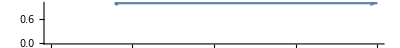
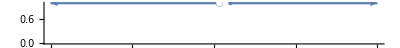
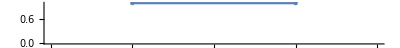
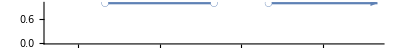
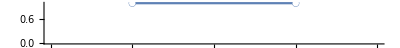
Lösningarna kan illustreras på en tallinje där lösningsmängden framgår antigen av en fylld punkt som betyder att det är större/mindre eller lika med, eller en ofylld punkt som belyser att det endast är större eller mindre än.

Lösningsmängder och visualisering:

a) LM={x≥2}

-Graphics-

b) LM = {x<1/3||x≥1}

-Graphics-

c) LM ={-2≤x≤2}

-Graphics-

d) LM ={-1<x<1||x≥2}

-Graphics-

e) LM ={-1<x<1}

-Graphics-

#### Uppgift 22

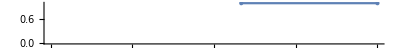
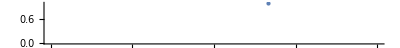
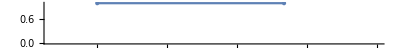
Lösningarna kan illustreras på en tallinje där lösningsmängden framgår antigen av en fylld punkt som betyder att det är större/mindre eller lika med, eller en ofylld punkt som belyser att det endast är större eller mindre än.

Lösningsmängd och visualisering:

a)  False (F, saknar lösning)

b) LM={1/2≤x≤3}

-Graphics-

c) LM ={x=1}

-Graphics-

d) LM ={0≤x≤4}

-Graphics-

#### Uppgift 25

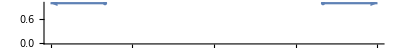
Lösningen kan illustreras på en tallinje där lösningsmängden framgår av antigen en fylld punkt som betyder att det är större/mindre eller lika med, eller en ofylld punkt som belyser att det endast är större eller mindre än.

Lösningsmängd och visualiering:

LM={x≤-2||x≥2}

-Graphics-

#### Uppgift 26

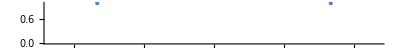
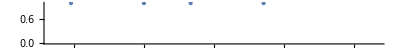
Lösningarna kan illustreras på en tallinje där lösningsmängden framgår av antigen en fylld punkt som betyder det är större/mindre eller lika med, eller en ofylld punkt som belyser att det endast är större eller mindre än.

Lösningsmängd och visualisering:

a) LM={{x=-1},{x=4}}

-Graphics-

b) LM={{x=0},{x=1},{x=1/2 (1-√17)},{x=1/2 (1+√17)}}


-Graphics-

## Kod

### Uppgift 21

För att bestämma lösningen till följande olikheter används funktionen “reduce”. För att sedan grafisk representera det på en tidslinje används “NumberLinePlot”.

a)

```mathematica
Reduce[(x-2)/(x^2+1)≥0]
NumberLinePlot[(x-2)/(x^2+1)≥0,{x,0, 10}]
```

b)

```mathematica
Reduce[2/(3x-1)≤1]
NumberLinePlot [2/(3x-1)≤1,{x,-10,10}]
```

c)

```mathematica
Reduce[4/(x^2+4)≥1/2]
NumberLinePlot[4/(x^2+4)≥1/2,{x,-4,4}]
```

d)

```mathematica
Reduce[(x-2)/(x^2-1)≥0]
NumberLinePlot[(x-2)/(x^2-1)>0,{x,-2, 4}]
```

e)

```mathematica
Reduce[(x-2)/(x-1)≥1+(2x)/(x+1)]
NumberLinePlot[(x-2)/(x-1)>1 + ((2x)/(x+1)),{x,-2, 2}]
```

### Uppgift 22

För att bestämma lösningen till följande olikheter används funktionen reduce. För att sedan grafisk representera det på en tidslinje används “NumberLinePlot”.
a)

```mathematica
Reduce[√(x+1)≤-√(2+x)]
```

b)

```mathematica
Reduce [√(2x-1)>-√(3-x)]
NumberLinePlot[(√(2x-1))>(-√(3-x)),{x,-3, 3}]
```

c)

```mathematica
Reduce [√(x^2-1)≥√(2 x^2-2x)]
NumberLinePlot[(√(x^2-1))≥(√(2 x^2-2x)),{x,-3, 3}]
```

d)

```mathematica
Reduce[2+√x≥x]
NumberLinePlot[2+√x≥ (x), {x,-1, 6}]
```

### Uppgift 25

För att bestämma lösningen till följande olikhet används funktionen reduce. För att sedan grafisk representera det på en tidslinje används “NumberLinePlot”.

```mathematica
Reduce[(x^2+1)^2-4(x^2+1)≥5,x,Reals]
NumberLinePlot[(x^2+1)^2-4(x^2+1)≥5, {x,-3, 3}]
```

### Uppgift 26

För att bestämma lösningen till följande olikheter används funktionen reduce. För att sedan grafisk representera det på en tidslinje används “NumberLinePlot”.
a)

```mathematica
Solve[Abs [x-1]+Abs [x-2]==5]
NumberLinePlot[(Abs[x-1]+Abs[x-2])== 5,{x,-2,5}]
```

b)

```mathematica
Solve[Abs[x^2-x-2]==2,x]
NumberLinePlot [Abs[x^2-x-2]==2,{x, -2,5}]
```

## Diskussion

Resultatet på uppgift 21 börjar med att först bestämma lösningar till olikheterna, och dessa representeras sedan grafiskt. Under “Resultat” ser man hur varje olikhet, beroende på olikhetstecknet (dvs om det är ≤, ≥, <, >), har en ifylld prick eller ej, samt om linjen har en fortsatt pil eller ej för värdet på x. Samma princip följer genom resterande uppgifter och i uppgift 26 visas grafen med endast prickar utan intervall-linjer, det beror på att värdet för x är absolut satt och inte i olikhet.

Uppgift 3: Binomisk Ekvation

## Sammanfattning

### Uppgift

Finn lösningen till ekvationen z^5=-3+3i och visa grafiskt att dessa ligger på en cirkel i komplexa talplanet.

### Resultat

Lösningsmängd:

LM = {(-3+3ⅈ)^(1/5), (-3+3ⅈ)^(1/5)(-1)^(2/5), -(-3+3ⅈ)^(1/5)(-1)^(3/5), (-3+3ⅈ)^(1/5)(-1)^(4/5), -(-3)^(1/5) (-1+ⅈ)^(1/5)}

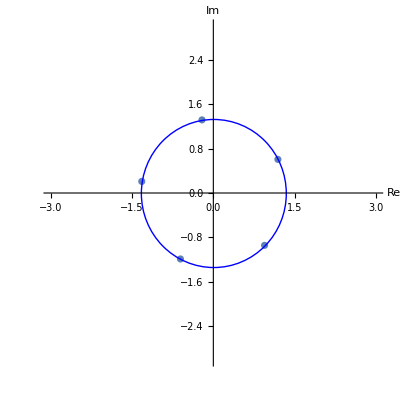
Visualisering:
-Graphics-

## Kod

För att bestämma lösningarna på ekvationen används följande funktion:

```mathematica
Solve[z^5== -3+3I];
```

För att sedan grafiskt representera komplexa talplanet används ListPlot. Därför samlas lösningarna i en lista genom att först definiera talen med en variabel:

```mathematica
z1= (-3+3ⅈ)^(1/5);
z2= (-3+3ⅈ)^(1/5) (-1)^(2/5);
z3= -(-3+3ⅈ)^(1/5) (-1)^(4/5);
z4= (-3+3ⅈ)^(1/5) (-1)^(4/5);
z5=-(-3)^(1/5) (-1+ⅈ)^(1/5);
```

Därefter inmatas talen i en lista som definieras med valfri variabel:

```mathematica
cn={z1,z2,z3,z4,z5};
```

Därefter konverteras tallistan till talparslista; realdel och imaginärdel, i syfte att få talens rektangulärform samt representeras i en komplex talplan.

Det sker genom “Table”-funktion där man även anger antalet gånger den ska gå igenom listan (i-min och i-max):

```mathematica
pp=Table[{Re[cn[[i]]], Im[cn[[i]]]}, {i,1,5}];
```

Före ritning av talen ska man ta reda på radien av talen i syfte att ange radien som cirkeln ska ritas med. Här används pythagoras sats:

r= √(a^2+b^2)

För att utföra det krävs endast att ett av talen, i det här fallet z1, i sin rektangulära form väljs:

z1 = 1.18962 + 0.606141 i

```mathematica
Solve[r==√(1.189619664737166^2+0.6061414944026161^2)];
{{r->1.335141362540313}}
```

Slutligen ska cirkeln visualiseras med angiven radie:

```mathematica
Epilog->{PointSize[0.02],Blue,Circle[{0,0},{1.335141362540313, 1.335141362540313}]
```

## Diskussion

Eftersom ekvationen är av grad 5 innebär det att det finns fem lösningar i det komplexa talplanet. Resultatet visar hur man omvandlar till rektangulär för att beräkna avstånd från koordinaten till origo, dvs radien med hjälp av phytagoras sats. Resultaten är en cirkel med tillhörande fem spridda koordinater, där cirkeln r visas som ovan resultat från origo.

Uppgift 4 : Arean av en cirkel och närmevärde till Pi

## Sammanfattning

### Uppgift

En kvadrat kan skrivas in i en cirkel och en cirkel kan skrivas in i en kvadrat, vilket ger figuren nedan. Antag att cirkeln har radien r = 1

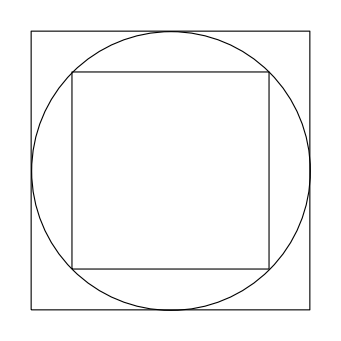
```mathematica
Show[Graphics[{FaceForm[None],EdgeForm[{Black}],Polygon[{{-1/Sqrt[2],-1/Sqrt[2]},{-1/Sqrt[2],1/Sqrt[2]},{1/Sqrt[2],1/Sqrt[2]} ,{1/Sqrt[2], -1/Sqrt[2]}}],Disk[{0, 0}],Polygon[{{-1, -1}, {-1, 1},{1, 1},{1, -1}}]}]]
-Graphics-
```

Från figuren kan vi konstatera att cirkelns area är mindre än 2^2=4 och större än (2/√2)^2=2. Det betyder att vi kan bestämma π=3±1. Dvs medelvärdet av 4+2 och det absoluta felet till närmevärdet. Då cirkelns area i detta fall är π r^2= π, så är detta också en metod att bestämma ett närmevärde till π. 
Vi kan också se arean för en kvadrat som fyrsidig polygon där arean kan bestämmas av fyra trianglar.
Använd ovanstående metod med reglebundna polygoner med fler sidor än fyra och beräkna ett mer exakt värde på π. Jämför sedan med värdet på Pi i Mathematica (se nedan med 10 siffor). Du får använda trigonometriska funktioner för att bestämma arean av trianglarna. 
Rita en graf för hur min och max värdet konvergerar mot Pi som en funktion av antal sidor på polygonen.

```mathematica
N[Pi, 10]
```

```mathematica
3.141592654
```

### Resultat

A av regelbunden polygon

A av regelbunden polygon

A av regelbundna polygon

## Kod

Först definieras arean av den mindre polygonen som en funktion av antalet sidor [x] och den tilldelas variabeln p1 :

```mathematica
p1=f[x_]=x/2×Sin[(360°)/x]
```

Därefter definieras arean av den stora polygonen som en funktion av antalet sidor x och den tilldelas variabeln p2 :

```mathematica
p2=f[x_]=(1/2)x×2×1×Tan[(180°)/x]×1
```

Nästa steg är att visa funktionen som en graf, y - axeln är polygonens area och x - axeln är antalet sidor av polygonen:

```mathematica
Plot[p1,{x,3,10000}]
```

Följande steg har samma beskrivning som ovan :

```mathematica
Plot[p2,{x,3,10 000}]
```

Variabeln [pa] tilldelas grafen, linjen tilldelas  grön färg och högre tjocklek för linje, x - axeln tilldelas sidor och y - axeln area samt att grafen visar funktionen i intervallet x = 0 till 10000 och y = 3.14158 till 3.14160 :

```mathematica
pa=Plot[p1,{x,3,10000},PlotStyle->{Green,Thick},AxesLabel->{“Antal sidor”,“Area av regelbunden polygon”},PlotRange->{{0,10000},{3.14158,3.14160}}]
```

Variabeln [pb] tilldelas grafen, blå färg och högre tjocklek för linje, x - axeln tilldelas sidor och y - axeln area samt att grafen visar funktionen mellan x = 0 till 10000 och y = 3.14158 till 3.14160:

```mathematica
pb=Plot[p2,{x,3,10000},PlotStyle->{Blue,Thick},AxesLabel->{“Antal sidor”,“Area av regelbunden polygon”}]
```

Tilldelar π variabeln p3:

```mathematica
p3=Pi
```

Grafen av π visas som en konstant mellan ovannämnda x - värden och färgväl och tjocklek justeras :

```mathematica
pc=Plot[p3,{x,0,10000},PlotStyle->{Red,Thick}]
```

Samtliga grafer samlade mellan ovannämnda x och y - värden :

```mathematica
Show[pa,pb,pc,AxesLabel->{“Antal sidor”,“Area av regelbunden polygon”},PlotRange->{{0,10000},{3.14158,3.14160}}]
```

## Diskussion

Inlednigsvis används regelbundna polygoner,som definieras av n≥3 sida av samma längd och att samtliga vinklar är 360/n stora,för att erhålla ett värde på cirkeln.Eftersom cirkeln har r=1 ritas den in i polygon med n sidor och en polygen ritas in med n sidor i cirkeln,därefter erhålls areans medelvärde av både större och mindre polygonen för att sedan erhålla ett närmevärde till π.Sedan räknas arean av större och mindre polygonen med hjälp av trigonometri,som grafiskt formuleras i hur det närmevärdet är till π.